12

0

-84

-84

True

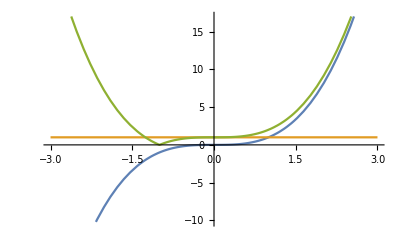

12

0

-84

-84

True

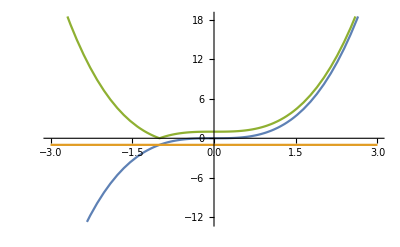

-12

-1

-84

-84

True

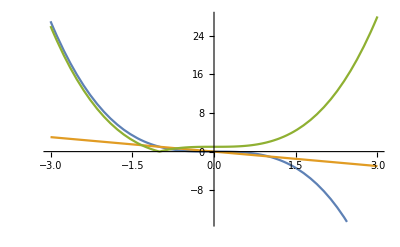

```mathematica
ClearAll["Global`*"]


a=t^3;
b=1;
c=Abs[a+b];

D[a,t]/.t->-2
D[b,t]/.t->-2
Original=D[c,t]/.t->-2
Modified=D[c,t]/.Abs'->Abs/.t->-2
Original===Modified
Plot[{a,b,c},{t,-3,3}]

x=t^3;
y=-1;
z=Abs[a+b];

D[x,t]/.t->-2
D[y,t]/.t->-2
Original=D[z,t]/.t->-2
Modified=D[z,t]/.Abs'->Abs/.t->-2
Original===Modified
Plot[{x,y,z},{t,-3,3}]


x=-t^3;
y=-t;
z=Abs[a+b];

D[x,t]/.t->-2
D[y,t]/.t->-2
Original=D[z,t]/.t->-2
Modified=D[z,t]/.Abs'->Abs/.t->-2
Original===Modified
Plot[{x,y,z},{t,-3,3}]
```

```mathematica
f[x_]:=Piecewise[{{x,x>0},{-x,x<0}}]
Abs'[x_]:=D[f[x],t]
```